-Graphics-

Reduce::naqs: {x+4 y≤24,x+y≤9,21-3 x-y≥0,x≥0,y≥0}&&(x|y)∈ℝ is not a quantified system of equations and inequalities.

FindInstance::naqs: Reduce[{x+4 y≤24,x+y≤9,21-3 x-y≥0,x≥0,y≥0}&&(x|y)∈ℝ,{x,y},ℝ] is not a quantified system of equations and inequalities.

ReplaceAll::reps: {FindInstance[Reduce[{x+Times[«2»]≤24,x+y≤9,21+Times[«2»]+Times[«2»]≥0,x≥0,y≥0}&&(x|y)∈ℝ,{x,y},ℝ],{x,y},ℝ]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x,y}/.FindInstance[Reduce[{x+4 y≤24,x+y≤9,21-3 x-y≥0,x≥0,y≥0}&&(x|y)∈ℝ,{x,y},ℝ],{x,y},ℝ]

-Graphics-

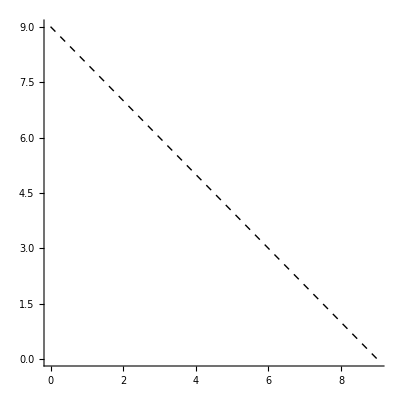

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{-3,-1},{{1,4},{1,1},{-3,-1},{-1,0},{0,-1}},{24,9,-21,0,0}]

-Graphics-

{21,{x→7,y→0}}

```mathematica
(* Задача 1: Линейно програмиране *)

(* Дефиниране на ограничителните условия *)
constraints = {
   x + 4 y ≤ 24,
   x + y ≤ 9,
   -3 x - y + 21 ≥ 0,
   x ≥ 0,
   y ≥ 0
   };

(* 1. Скициране на областта Ω *)
region = ImplicitRegion[And @@ constraints, {x, y}];
RegionPlot[region, {x, 0, 10}, {y, 0, 10},
 PlotStyle -> LightBlue,
 AxesLabel -> {"x", "y"},
 PlotLegends -> "Expressions",
 LabelStyle -> Large]

(* 2. Намиране на върховете на Ω *)
vertices = Reduce[constraints && (x | y) ∈ Reals, {x, y}, Reals];

corners = {x, y} /. FindInstance[vertices, {x, y}, Reals]



(* 3. Производствени планове и посока на нарастване на F(x, y) *)
contour = ContourPlot[3 x + y == 0, {x, 0, 10}, {y, 0, 10},
   ContourStyle -> Red, PlotRange -> All];
gradVector = Graphics[Arrow[{{0, 0}, {3, 1}}]];

Show[contour, gradVector, 
 RegionPlot[region, {x, 0, 10}, {y, 0, 10}, 
  PlotStyle -> LightBlue]]

(* 4. Анимация за оптимално решение *)
frames = Table[
   ContourPlot[3 x + y == c, {x, 0, 10}, {y, 0, 10},
    ContourStyle -> Red, PlotRange -> All], {c, 0, 30, 0.5}];
ListAnimate[frames]

(* 5. Решение с графичния метод *)
Graphics[{Dashed, Line[{{0, 9}, {9, 0}}]}, Axes -> True]

(* 6. Решение с LinearProgramming *)
objective = {3, 1}; (* Целева функция *)
matrix = {{1, 4}, {1, 1}, {-3, -1}, {-1, 0}, {0, -1}}; (* Коэффициенти *)
rhs = {24, 9, -21, 0, 0}; (* Дясна част *)
LinearProgramming[-objective, matrix, rhs]

(* 7. Всички решения *)
solution = Reduce[constraints, {x, y}, Reals];
solutionGraphics = RegionPlot[
   solution, {x, 0, 10}, {y, 0, 10}, 
   PlotStyle -> LightGreen];
Show[solutionGraphics]

(* 8. Решение с Reduce и Maximize *)
maxSolution = Maximize[{3 x + y, constraints}, {x, y}, Reals]
```